```mathematica
Clear["All`*"]
u1[x_,z_,t_] = E^z*Cos[x-t];
u2[x_,z_,t_] = E^z*Sin[x-t];
re = {x->x[t],z->z[t]};
eq1 = St*D[x[t],{t,2}]==St*(1/St*(eps*u1[x[t],z[t],t]-D[x[t],t])         +(b*eps*((D[u1[x,z,t],t]/.re)+D[x[t],t]*(D[u1[x,z,t],x]/.re)+D[x[t],t]*(D[u1[x,z,t],z])/.re)));
eq2 = St*D[x[t],{t,2}]==St*(1/St*(eps*u2[x[t],z[t],t]-D[z[t],t]-vS)+b*eps*((D[u2[x,z,t],t]/.re)+D[x[t],t]*(D[u2[x,z,t],x]/.re)+D[x[t],t]*(D[u2[x,z,t],z]/.re)));
Simplify[eq1]
Simplify[eq2]
sigma[t_]=Exp[z[t]-i*(x[t]-t)];
omega[t_] = D[x[t],t]-1+i*D[z[t],t]-b*eps*Exp[z[t]+i([x[t]-t])];
Clear["All`*"]
sysofeq = {-i*si*om-i*b*eps*si*sibar,
i*sibar*ombar+i*b*eps*sibar*si,
1/St*(eps*(1-b)*sibar-om-1-i*vS),
1/St*(eps*(1-b)*si-ombar-1+i*vS)};
jac = D[sysofeq,{{si,sibar,om,ombar}}];
sols = Solve[sysofeq == {0,0,0,0},{si,sibar,om,ombar}];
Eigenvalues[jac /. sols[[1]]]
Eigenvectors[jac /. sols[[1]]]
```

x'[t]+St x''[t]==ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) eps (Cos[t-x[t]]-b St Sin[t-x[t][t]]+b St (Cos[t-x[t]]+Sin[t-x[t][t]]) x[t]'[t])

vS+b ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) eps St Cos[t-x[t]]+ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) eps Sin[t-x[t]]+z00'[t]+delta z01'[t]+eps z10'[t]+delta eps z11'[t]+St x''[t]==b ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) eps St (Cos[t-x[t]]-Sin[t-x[t]]) x'[t]

We write H = H00 + eps H10 (can I write this as a function like H[0][1][T] or so? So H, X, z need to be 2x2 matrices of functions
FIRST ARGUMENT: eps
SECOND ARGUMENT: delta


no wait, H is just a function of X and z, we probably do not even have to write it explicitly(?) but can automatically expand? surely there is some good way to do this. Do it on paper first...

```mathematica
ClearAll["Global`*"]
A=eps (1-I b St-b St vS)/(1-I St-St vS);
Hs=-z+vS X+Exp[z] ComplexExpand[Re[A Exp[I X]]]; 
sub={X->X0[t],z->z0[t]};
sys={X0'[t]==(D[Hs,z]/. sub),z0'[t]==-(D[Hs,x]/. sub)};
Coefficient[D[Hs,z]/.sub,eps,0];
Awoeps = (1-I*b*St-b*St*vS)/(1-I*St-St*vS);
H[0][0][T_]=-z[0][0][T]+vS*X[0][0][T];
H[1][0][T_]=-z[1][0][T]+vS*X[1][0][T];
H[0][1][T_]=Exp[z[0][0][T]]*Real[Awoeps * Exp[I*X[0][0][T]]];
H[1][1][T_] =Exp[z[1][0][T]]*Real[Awoeps * Exp[I*X[0][0][T]]]+Exp[z[0][0][T]]*Real[I*Awoeps * Exp[I*X[1][0][T]]];
D[X[0][0][T],T] == D[H[0][0][T]]
```

X[0][0]'[T]==vSX[0][0][T]-z[0][0][T]

```mathematica
rules = {X ->( X00[#] + eps X10[#] + delta X01[#]+ eps delta X11[#]&),
z -> (z00[#] + eps z10[#] + delta z01[#]+ eps delta z11[#]&)};
H[X_,z_] = -z+vS X+Exp[z] ComplexExpand[Re[A Exp[I X]]]; 
dHdX[X_,z_] = D[H[X,z],X];
dHdz[X_,z_] = D[H[X,z],z];
Xp=X00+eps X10+delta X01+eps delta X11;
zp=z00+eps z10+delta z01+eps delta z11;

kappa = 1/(1-b)-b*St^2-I*b*St/(1-b);
sys = {-D[X[t],t] + dHdz[X[t],z[t]] + delta*Re[-I*Conjugate[kappa]]*Exp[2*z[t]],
	-D[z[t],t]  -dHdX[X[t],z[t] ]+delta*Im[-I*Conjugate[kappa]]*Exp[2*z[t]]};

sysP =sys/.rules
```

{-1+delta ⅇ^(2 (z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t])) (Im[b St^2]+Im[1/(1-Conjugate[b])]+Re[(b St)/(1-b)])+ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) ((eps Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(b eps St^2 Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(eps St vS Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(b eps St vS Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(b eps St^2 vS^2 Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(eps St Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(b eps St Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2))-X00'[t]-delta X01'[t]-eps X10'[t]-delta eps X11'[t],-vS+delta ⅇ^(2 (z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t])) (-Im[(b St)/(1-b)]+Re[b St^2]-Re[1/(1-Conjugate[b])])-ⅇ^(z00[t]+delta z01[t]+eps z10[t]+delta eps z11[t]) (-(eps St Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(b eps St Cos[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(eps Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(b eps St^2 Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(eps St vS Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)+(b eps St vS Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2)-(b eps St^2 vS^2 Sin[X00[t]+delta X01[t]+eps X10[t]+delta eps X11[t]])/(St^2+(1-St vS)^2))-z00'[t]-delta z01'[t]-eps z10'[t]-delta eps z11'[t]}

```mathematica
coef[expr_,i_,j_]:=(D[expr,{eps,i},{delta,j}]/(i! j!))/. {eps->0,delta->0};
eq00 = Thread[(coef[#,0,0]& /@ sysP) == 0];
sol00 = DSolve[Join[eq00,{X00[0]==0,z00[0]==0}],{X00,z00},t][[1]];
eq10 = Thread[(coef[#,1,0]& /@sysP) == 0]/. sol00;
sol10 = DSolve[Join[eq10,{X10[0]==0,z10[0]==0}],{X10,z10},t][[1]];
eq01 = Thread[(coef[#,0,1]& /@sysP) == 0] /. sol00/.sol10;
sol01 = DSolve[Join[eq01,{X01[0]==0,z01[0]==0}],{X01,z01},t][[1]];
eq11 = Thread[(coef[#,1,1]& /@sysP) == 0] /. sol00/.sol10/.sol01;
sol11 = DSolve[Join[eq11,{X11[0]==0,z11[0]==0}],{X11,z11},t][[1]]
```

{X11→Function[{t},(ⅇ^(-3 t vS) (2 ⅇ^(3 t vS) vS Im[(b St)/(1-b)]+2 b ⅇ^(3 t vS) St^2 vS Im[(b St)/(1-b)]-10 ⅇ^(3 t vS) St vS^2 Im[(b St)/(1-b)]+6 b ⅇ^(3 t vS) St vS^2 Im[(b St)/(1-b)]-6 ⅇ^(3 t vS) vS^3 Im[(b St)/(1-b)]-4 b ⅇ^(3 t vS) St^2 vS^3 Im[(b St)/(1-b)]+6 ⅇ^(3 t vS) St vS^4 Im[(b St)/(1-b)]+6 b ⅇ^(3 t vS) St vS^4 Im[(b St)/(1-b)]-6 b ⅇ^(3 t vS) St^2 vS^5 Im[(b St)/(1-b)]-St Cos[t] Im[(b St)/(1-b)]+b St Cos[t] Im[(b St)/(1-b)]+ⅇ^(2 t vS) St Cos[t] Im[(b St)/(1-b)]-b ⅇ^(2 t vS) St Cos[t] Im[(b St)/(1-b)]-3 vS Cos[t] Im[(b St)/(1-b)]+ⅇ^(2 t vS) vS Cos[t] Im[(b St)/(1-b)]-3 b St^2 vS Cos[t] Im[(b St)/(1-b)]+b ⅇ^(2 t vS) St^2 vS Cos[t] Im[(b St)/(1-b)]+2 St vS^2 Cos[t] Im[(b St)/(1-b)]+4 b St vS^2 Cos[t] Im[(b St)/(1-b)]+8 ⅇ^(2 t vS) St vS^2 Cos[t] Im[(b St)/(1-b)]-10 b ⅇ^(2 t vS) St vS^2 Cos[t] Im[(b St)/(1-b)]-3 vS^3 Cos[t] Im[(b St)/(1-b)]+9 ⅇ^(2 t vS) vS^3 Cos[t] Im[(b St)/(1-b)]-6 b St^2 vS^3 Cos[t] Im[(b St)/(1-b)]+10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Im[(b St)/(1-b)]+3 St vS^4 Cos[t] Im[(b St)/(1-b)]+3 b St vS^4 Cos[t] Im[(b St)/(1-b)]-9 ⅇ^(2 t vS) St vS^4 Cos[t] Im[(b St)/(1-b)]-9 b ⅇ^(2 t vS) St vS^4 Cos[t] Im[(b St)/(1-b)]-3 b St^2 vS^5 Cos[t] Im[(b St)/(1-b)]+9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Im[(b St)/(1-b)]+2 ⅇ^(t vS) Im[b St^2]-2 ⅇ^(3 t vS) Im[b St^2]+2 b ⅇ^(t vS) St^2 Im[b St^2]-2 b ⅇ^(3 t vS) St^2 Im[b St^2]-4 ⅇ^(t vS) St vS Im[b St^2]+10 ⅇ^(3 t vS) St vS Im[b St^2]-6 b ⅇ^(3 t vS) St vS Im[b St^2]+18 ⅇ^(t vS) vS^2 Im[b St^2]+6 ⅇ^(3 t vS) vS^2 Im[b St^2]+20 b ⅇ^(t vS) St^2 vS^2 Im[b St^2]+4 b ⅇ^(3 t vS) St^2 vS^2 Im[b St^2]-36 ⅇ^(t vS) St vS^3 Im[b St^2]-6 ⅇ^(3 t vS) St vS^3 Im[b St^2]-6 b ⅇ^(3 t vS) St vS^3 Im[b St^2]+18 b ⅇ^(t vS) St^2 vS^4 Im[b St^2]+6 b ⅇ^(3 t vS) St^2 vS^4 Im[b St^2]+Cos[t] Im[b St^2]-ⅇ^(2 t vS) Cos[t] Im[b St^2]+b St^2 Cos[t] Im[b St^2]-b ⅇ^(2 t vS) St^2 Cos[t] Im[b St^2]-8 St vS Cos[t] Im[b St^2]+6 b St vS Cos[t] Im[b St^2]+2 ⅇ^(2 t vS) St vS Cos[t] Im[b St^2]-15 vS^2 Cos[t] Im[b St^2]-9 ⅇ^(2 t vS) vS^2 Cos[t] Im[b St^2]-14 b St^2 vS^2 Cos[t] Im[b St^2]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Im[b St^2]+24 St vS^3 Cos[t] Im[b St^2]+6 b St vS^3 Cos[t] Im[b St^2]+18 ⅇ^(2 t vS) St vS^3 Cos[t] Im[b St^2]-15 b St^2 vS^4 Cos[t] Im[b St^2]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Im[b St^2]+2 ⅇ^(t vS) Im[1/(1-Conjugate[b])]-2 ⅇ^(3 t vS) Im[1/(1-Conjugate[b])]+2 b ⅇ^(t vS) St^2 Im[1/(1-Conjugate[b])]-2 b ⅇ^(3 t vS) St^2 Im[1/(1-Conjugate[b])]-4 ⅇ^(t vS) St vS Im[1/(1-Conjugate[b])]+10 ⅇ^(3 t vS) St vS Im[1/(1-Conjugate[b])]-6 b ⅇ^(3 t vS) St vS Im[1/(1-Conjugate[b])]+18 ⅇ^(t vS) vS^2 Im[1/(1-Conjugate[b])]+6 ⅇ^(3 t vS) vS^2 Im[1/(1-Conjugate[b])]+20 b ⅇ^(t vS) St^2 vS^2 Im[1/(1-Conjugate[b])]+4 b ⅇ^(3 t vS) St^2 vS^2 Im[1/(1-Conjugate[b])]-36 ⅇ^(t vS) St vS^3 Im[1/(1-Conjugate[b])]-6 ⅇ^(3 t vS) St vS^3 Im[1/(1-Conjugate[b])]-6 b ⅇ^(3 t vS) St vS^3 Im[1/(1-Conjugate[b])]+18 b ⅇ^(t vS) St^2 vS^4 Im[1/(1-Conjugate[b])]+6 b ⅇ^(3 t vS) St^2 vS^4 Im[1/(1-Conjugate[b])]+Cos[t] Im[1/(1-Conjugate[b])]-ⅇ^(2 t vS) Cos[t] Im[1/(1-Conjugate[b])]+b St^2 Cos[t] Im[1/(1-Conjugate[b])]-b ⅇ^(2 t vS) St^2 Cos[t] Im[1/(1-Conjugate[b])]-8 St vS Cos[t] Im[1/(1-Conjugate[b])]+6 b St vS Cos[t] Im[1/(1-Conjugate[b])]+2 ⅇ^(2 t vS) St vS Cos[t] Im[1/(1-Conjugate[b])]-15 vS^2 Cos[t] Im[1/(1-Conjugate[b])]-9 ⅇ^(2 t vS) vS^2 Cos[t] Im[1/(1-Conjugate[b])]-14 b St^2 vS^2 Cos[t] Im[1/(1-Conjugate[b])]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Im[1/(1-Conjugate[b])]+24 St vS^3 Cos[t] Im[1/(1-Conjugate[b])]+6 b St vS^3 Cos[t] Im[1/(1-Conjugate[b])]+18 ⅇ^(2 t vS) St vS^3 Cos[t] Im[1/(1-Conjugate[b])]-15 b St^2 vS^4 Cos[t] Im[1/(1-Conjugate[b])]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Im[1/(1-Conjugate[b])]+2 ⅇ^(t vS) Re[(b St)/(1-b)]-2 ⅇ^(3 t vS) Re[(b St)/(1-b)]+2 b ⅇ^(t vS) St^2 Re[(b St)/(1-b)]-2 b ⅇ^(3 t vS) St^2 Re[(b St)/(1-b)]-4 ⅇ^(t vS) St vS Re[(b St)/(1-b)]+10 ⅇ^(3 t vS) St vS Re[(b St)/(1-b)]-6 b ⅇ^(3 t vS) St vS Re[(b St)/(1-b)]+18 ⅇ^(t vS) vS^2 Re[(b St)/(1-b)]+6 ⅇ^(3 t vS) vS^2 Re[(b St)/(1-b)]+20 b ⅇ^(t vS) St^2 vS^2 Re[(b St)/(1-b)]+4 b ⅇ^(3 t vS) St^2 vS^2 Re[(b St)/(1-b)]-36 ⅇ^(t vS) St vS^3 Re[(b St)/(1-b)]-6 ⅇ^(3 t vS) St vS^3 Re[(b St)/(1-b)]-6 b ⅇ^(3 t vS) St vS^3 Re[(b St)/(1-b)]+18 b ⅇ^(t vS) St^2 vS^4 Re[(b St)/(1-b)]+6 b ⅇ^(3 t vS) St^2 vS^4 Re[(b St)/(1-b)]+Cos[t] Re[(b St)/(1-b)]-ⅇ^(2 t vS) Cos[t] Re[(b St)/(1-b)]+b St^2 Cos[t] Re[(b St)/(1-b)]-b ⅇ^(2 t vS) St^2 Cos[t] Re[(b St)/(1-b)]-8 St vS Cos[t] Re[(b St)/(1-b)]+6 b St vS Cos[t] Re[(b St)/(1-b)]+2 ⅇ^(2 t vS) St vS Cos[t] Re[(b St)/(1-b)]-15 vS^2 Cos[t] Re[(b St)/(1-b)]-9 ⅇ^(2 t vS) vS^2 Cos[t] Re[(b St)/(1-b)]-14 b St^2 vS^2 Cos[t] Re[(b St)/(1-b)]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Re[(b St)/(1-b)]+24 St vS^3 Cos[t] Re[(b St)/(1-b)]+6 b St vS^3 Cos[t] Re[(b St)/(1-b)]+18 ⅇ^(2 t vS) St vS^3 Cos[t] Re[(b St)/(1-b)]-15 b St^2 vS^4 Cos[t] Re[(b St)/(1-b)]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Re[(b St)/(1-b)]-2 ⅇ^(3 t vS) vS Re[b St^2]-2 b ⅇ^(3 t vS) St^2 vS Re[b St^2]+10 ⅇ^(3 t vS) St vS^2 Re[b St^2]-6 b ⅇ^(3 t vS) St vS^2 Re[b St^2]+6 ⅇ^(3 t vS) vS^3 Re[b St^2]+4 b ⅇ^(3 t vS) St^2 vS^3 Re[b St^2]-6 ⅇ^(3 t vS) St vS^4 Re[b St^2]-6 b ⅇ^(3 t vS) St vS^4 Re[b St^2]+6 b ⅇ^(3 t vS) St^2 vS^5 Re[b St^2]+St Cos[t] Re[b St^2]-b St Cos[t] Re[b St^2]-ⅇ^(2 t vS) St Cos[t] Re[b St^2]+b ⅇ^(2 t vS) St Cos[t] Re[b St^2]+3 vS Cos[t] Re[b St^2]-ⅇ^(2 t vS) vS Cos[t] Re[b St^2]+3 b St^2 vS Cos[t] Re[b St^2]-b ⅇ^(2 t vS) St^2 vS Cos[t] Re[b St^2]-2 St vS^2 Cos[t] Re[b St^2]-4 b St vS^2 Cos[t] Re[b St^2]-8 ⅇ^(2 t vS) St vS^2 Cos[t] Re[b St^2]+10 b ⅇ^(2 t vS) St vS^2 Cos[t] Re[b St^2]+3 vS^3 Cos[t] Re[b St^2]-9 ⅇ^(2 t vS) vS^3 Cos[t] Re[b St^2]+6 b St^2 vS^3 Cos[t] Re[b St^2]-10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Re[b St^2]-3 St vS^4 Cos[t] Re[b St^2]-3 b St vS^4 Cos[t] Re[b St^2]+9 ⅇ^(2 t vS) St vS^4 Cos[t] Re[b St^2]+9 b ⅇ^(2 t vS) St vS^4 Cos[t] Re[b St^2]+3 b St^2 vS^5 Cos[t] Re[b St^2]-9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Re[b St^2]+2 ⅇ^(3 t vS) vS Re[1/(1-Conjugate[b])]+2 b ⅇ^(3 t vS) St^2 vS Re[1/(1-Conjugate[b])]-10 ⅇ^(3 t vS) St vS^2 Re[1/(1-Conjugate[b])]+6 b ⅇ^(3 t vS) St vS^2 Re[1/(1-Conjugate[b])]-6 ⅇ^(3 t vS) vS^3 Re[1/(1-Conjugate[b])]-4 b ⅇ^(3 t vS) St^2 vS^3 Re[1/(1-Conjugate[b])]+6 ⅇ^(3 t vS) St vS^4 Re[1/(1-Conjugate[b])]+6 b ⅇ^(3 t vS) St vS^4 Re[1/(1-Conjugate[b])]-6 b ⅇ^(3 t vS) St^2 vS^5 Re[1/(1-Conjugate[b])]-St Cos[t] Re[1/(1-Conjugate[b])]+b St Cos[t] Re[1/(1-Conjugate[b])]+ⅇ^(2 t vS) St Cos[t] Re[1/(1-Conjugate[b])]-b ⅇ^(2 t vS) St Cos[t] Re[1/(1-Conjugate[b])]-3 vS Cos[t] Re[1/(1-Conjugate[b])]+ⅇ^(2 t vS) vS Cos[t] Re[1/(1-Conjugate[b])]-3 b St^2 vS Cos[t] Re[1/(1-Conjugate[b])]+b ⅇ^(2 t vS) St^2 vS Cos[t] Re[1/(1-Conjugate[b])]+2 St vS^2 Cos[t] Re[1/(1-Conjugate[b])]+4 b St vS^2 Cos[t] Re[1/(1-Conjugate[b])]+8 ⅇ^(2 t vS) St vS^2 Cos[t] Re[1/(1-Conjugate[b])]-10 b ⅇ^(2 t vS) St vS^2 Cos[t] Re[1/(1-Conjugate[b])]-3 vS^3 Cos[t] Re[1/(1-Conjugate[b])]+9 ⅇ^(2 t vS) vS^3 Cos[t] Re[1/(1-Conjugate[b])]-6 b St^2 vS^3 Cos[t] Re[1/(1-Conjugate[b])]+10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Re[1/(1-Conjugate[b])]+3 St vS^4 Cos[t] Re[1/(1-Conjugate[b])]+3 b St vS^4 Cos[t] Re[1/(1-Conjugate[b])]-9 ⅇ^(2 t vS) St vS^4 Cos[t] Re[1/(1-Conjugate[b])]-9 b ⅇ^(2 t vS) St vS^4 Cos[t] Re[1/(1-Conjugate[b])]-3 b St^2 vS^5 Cos[t] Re[1/(1-Conjugate[b])]+9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Re[1/(1-Conjugate[b])]+Im[(b St)/(1-b)] Sin[t]-ⅇ^(2 t vS) Im[(b St)/(1-b)] Sin[t]+b St^2 Im[(b St)/(1-b)] Sin[t]-b ⅇ^(2 t vS) St^2 Im[(b St)/(1-b)] Sin[t]-4 St vS Im[(b St)/(1-b)] Sin[t]+2 b St vS Im[(b St)/(1-b)] Sin[t]+2 ⅇ^(2 t vS) St vS Im[(b St)/(1-b)] Sin[t]+vS^2 Im[(b St)/(1-b)] Sin[t]-9 ⅇ^(2 t vS) vS^2 Im[(b St)/(1-b)] Sin[t]+2 b St^2 vS^2 Im[(b St)/(1-b)] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^2 Im[(b St)/(1-b)] Sin[t]-4 St vS^3 Im[(b St)/(1-b)] Sin[t]+2 b St vS^3 Im[(b St)/(1-b)] Sin[t]+18 ⅇ^(2 t vS) St vS^3 Im[(b St)/(1-b)] Sin[t]+b St^2 vS^4 Im[(b St)/(1-b)] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^4 Im[(b St)/(1-b)] Sin[t]+St Im[b St^2] Sin[t]-b St Im[b St^2] Sin[t]-ⅇ^(2 t vS) St Im[b St^2] Sin[t]+b ⅇ^(2 t vS) St Im[b St^2] Sin[t]+7 vS Im[b St^2] Sin[t]-ⅇ^(2 t vS) vS Im[b St^2] Sin[t]+7 b St^2 vS Im[b St^2] Sin[t]-b ⅇ^(2 t vS) St^2 vS Im[b St^2] Sin[t]-22 St vS^2 Im[b St^2] Sin[t]+8 b St vS^2 Im[b St^2] Sin[t]-8 ⅇ^(2 t vS) St vS^2 Im[b St^2] Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Im[b St^2] Sin[t]-9 vS^3 Im[b St^2] Sin[t]-9 ⅇ^(2 t vS) vS^3 Im[b St^2] Sin[t]-2 b St^2 vS^3 Im[b St^2] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Im[b St^2] Sin[t]+9 St vS^4 Im[b St^2] Sin[t]+9 b St vS^4 Im[b St^2] Sin[t]+9 ⅇ^(2 t vS) St vS^4 Im[b St^2] Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Im[b St^2] Sin[t]-9 b St^2 vS^5 Im[b St^2] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Im[b St^2] Sin[t]+St Im[1/(1-Conjugate[b])] Sin[t]-b St Im[1/(1-Conjugate[b])] Sin[t]-ⅇ^(2 t vS) St Im[1/(1-Conjugate[b])] Sin[t]+b ⅇ^(2 t vS) St Im[1/(1-Conjugate[b])] Sin[t]+7 vS Im[1/(1-Conjugate[b])] Sin[t]-ⅇ^(2 t vS) vS Im[1/(1-Conjugate[b])] Sin[t]+7 b St^2 vS Im[1/(1-Conjugate[b])] Sin[t]-b ⅇ^(2 t vS) St^2 vS Im[1/(1-Conjugate[b])] Sin[t]-22 St vS^2 Im[1/(1-Conjugate[b])] Sin[t]+8 b St vS^2 Im[1/(1-Conjugate[b])] Sin[t]-8 ⅇ^(2 t vS) St vS^2 Im[1/(1-Conjugate[b])] Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Im[1/(1-Conjugate[b])] Sin[t]-9 vS^3 Im[1/(1-Conjugate[b])] Sin[t]-9 ⅇ^(2 t vS) vS^3 Im[1/(1-Conjugate[b])] Sin[t]-2 b St^2 vS^3 Im[1/(1-Conjugate[b])] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Im[1/(1-Conjugate[b])] Sin[t]+9 St vS^4 Im[1/(1-Conjugate[b])] Sin[t]+9 b St vS^4 Im[1/(1-Conjugate[b])] Sin[t]+9 ⅇ^(2 t vS) St vS^4 Im[1/(1-Conjugate[b])] Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Im[1/(1-Conjugate[b])] Sin[t]-9 b St^2 vS^5 Im[1/(1-Conjugate[b])] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Im[1/(1-Conjugate[b])] Sin[t]+St Re[(b St)/(1-b)] Sin[t]-b St Re[(b St)/(1-b)] Sin[t]-ⅇ^(2 t vS) St Re[(b St)/(1-b)] Sin[t]+b ⅇ^(2 t vS) St Re[(b St)/(1-b)] Sin[t]+7 vS Re[(b St)/(1-b)] Sin[t]-ⅇ^(2 t vS) vS Re[(b St)/(1-b)] Sin[t]+7 b St^2 vS Re[(b St)/(1-b)] Sin[t]-b ⅇ^(2 t vS) St^2 vS Re[(b St)/(1-b)] Sin[t]-22 St vS^2 Re[(b St)/(1-b)] Sin[t]+8 b St vS^2 Re[(b St)/(1-b)] Sin[t]-8 ⅇ^(2 t vS) St vS^2 Re[(b St)/(1-b)] Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Re[(b St)/(1-b)] Sin[t]-9 vS^3 Re[(b St)/(1-b)] Sin[t]-9 ⅇ^(2 t vS) vS^3 Re[(b St)/(1-b)] Sin[t]-2 b St^2 vS^3 Re[(b St)/(1-b)] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Re[(b St)/(1-b)] Sin[t]+9 St vS^4 Re[(b St)/(1-b)] Sin[t]+9 b St vS^4 Re[(b St)/(1-b)] Sin[t]+9 ⅇ^(2 t vS) St vS^4 Re[(b St)/(1-b)] Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Re[(b St)/(1-b)] Sin[t]-9 b St^2 vS^5 Re[(b St)/(1-b)] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Re[(b St)/(1-b)] Sin[t]-Re[b St^2] Sin[t]+ⅇ^(2 t vS) Re[b St^2] Sin[t]-b St^2 Re[b St^2] Sin[t]+b ⅇ^(2 t vS) St^2 Re[b St^2] Sin[t]+4 St vS Re[b St^2] Sin[t]-2 b St vS Re[b St^2] Sin[t]-2 ⅇ^(2 t vS) St vS Re[b St^2] Sin[t]-vS^2 Re[b St^2] Sin[t]+9 ⅇ^(2 t vS) vS^2 Re[b St^2] Sin[t]-2 b St^2 vS^2 Re[b St^2] Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^2 Re[b St^2] Sin[t]+4 St vS^3 Re[b St^2] Sin[t]-2 b St vS^3 Re[b St^2] Sin[t]-18 ⅇ^(2 t vS) St vS^3 Re[b St^2] Sin[t]-b St^2 vS^4 Re[b St^2] Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^4 Re[b St^2] Sin[t]+Re[1/(1-Conjugate[b])] Sin[t]-ⅇ^(2 t vS) Re[1/(1-Conjugate[b])] Sin[t]+b St^2 Re[1/(1-Conjugate[b])] Sin[t]-b ⅇ^(2 t vS) St^2 Re[1/(1-Conjugate[b])] Sin[t]-4 St vS Re[1/(1-Conjugate[b])] Sin[t]+2 b St vS Re[1/(1-Conjugate[b])] Sin[t]+2 ⅇ^(2 t vS) St vS Re[1/(1-Conjugate[b])] Sin[t]+vS^2 Re[1/(1-Conjugate[b])] Sin[t]-9 ⅇ^(2 t vS) vS^2 Re[1/(1-Conjugate[b])] Sin[t]+2 b St^2 vS^2 Re[1/(1-Conjugate[b])] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^2 Re[1/(1-Conjugate[b])] Sin[t]-4 St vS^3 Re[1/(1-Conjugate[b])] Sin[t]+2 b St vS^3 Re[1/(1-Conjugate[b])] Sin[t]+18 ⅇ^(2 t vS) St vS^3 Re[1/(1-Conjugate[b])] Sin[t]+b St^2 vS^4 Re[1/(1-Conjugate[b])] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^4 Re[1/(1-Conjugate[b])] Sin[t]))/(2 vS (1+vS^2) (1+9 vS^2) (1+St^2-2 St vS+St^2 vS^2))],z11→Function[{t},(ⅇ^(-3 t vS) (-2 ⅇ^(t vS) Im[(b St)/(1-b)]+2 ⅇ^(3 t vS) Im[(b St)/(1-b)]-2 b ⅇ^(t vS) St^2 Im[(b St)/(1-b)]+2 b ⅇ^(3 t vS) St^2 Im[(b St)/(1-b)]+4 ⅇ^(t vS) St vS Im[(b St)/(1-b)]-6 ⅇ^(3 t vS) St vS Im[(b St)/(1-b)]+2 b ⅇ^(3 t vS) St vS Im[(b St)/(1-b)]-18 ⅇ^(t vS) vS^2 Im[(b St)/(1-b)]+10 ⅇ^(3 t vS) vS^2 Im[(b St)/(1-b)]-20 b ⅇ^(t vS) St^2 vS^2 Im[(b St)/(1-b)]+12 b ⅇ^(3 t vS) St^2 vS^2 Im[(b St)/(1-b)]+36 ⅇ^(t vS) St vS^3 Im[(b St)/(1-b)]-22 ⅇ^(3 t vS) St vS^3 Im[(b St)/(1-b)]+2 b ⅇ^(3 t vS) St vS^3 Im[(b St)/(1-b)]-18 b ⅇ^(t vS) St^2 vS^4 Im[(b St)/(1-b)]+10 b ⅇ^(3 t vS) St^2 vS^4 Im[(b St)/(1-b)]+Cos[t] Im[(b St)/(1-b)]-ⅇ^(2 t vS) Cos[t] Im[(b St)/(1-b)]+b St^2 Cos[t] Im[(b St)/(1-b)]-b ⅇ^(2 t vS) St^2 Cos[t] Im[(b St)/(1-b)]-2 b St vS Cos[t] Im[(b St)/(1-b)]+2 ⅇ^(2 t vS) St vS Cos[t] Im[(b St)/(1-b)]+17 vS^2 Cos[t] Im[(b St)/(1-b)]-9 ⅇ^(2 t vS) vS^2 Cos[t] Im[(b St)/(1-b)]+18 b St^2 vS^2 Cos[t] Im[(b St)/(1-b)]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Im[(b St)/(1-b)]-32 St vS^3 Cos[t] Im[(b St)/(1-b)]-2 b St vS^3 Cos[t] Im[(b St)/(1-b)]+18 ⅇ^(2 t vS) St vS^3 Cos[t] Im[(b St)/(1-b)]+17 b St^2 vS^4 Cos[t] Im[(b St)/(1-b)]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Im[(b St)/(1-b)]-2 ⅇ^(3 t vS) vS Im[b St^2]-2 b ⅇ^(3 t vS) St^2 vS Im[b St^2]+10 ⅇ^(3 t vS) St vS^2 Im[b St^2]-6 b ⅇ^(3 t vS) St vS^2 Im[b St^2]+6 ⅇ^(3 t vS) vS^3 Im[b St^2]+4 b ⅇ^(3 t vS) St^2 vS^3 Im[b St^2]-6 ⅇ^(3 t vS) St vS^4 Im[b St^2]-6 b ⅇ^(3 t vS) St vS^4 Im[b St^2]+6 b ⅇ^(3 t vS) St^2 vS^5 Im[b St^2]+St Cos[t] Im[b St^2]-b St Cos[t] Im[b St^2]-ⅇ^(2 t vS) St Cos[t] Im[b St^2]+b ⅇ^(2 t vS) St Cos[t] Im[b St^2]+3 vS Cos[t] Im[b St^2]-ⅇ^(2 t vS) vS Cos[t] Im[b St^2]+3 b St^2 vS Cos[t] Im[b St^2]-b ⅇ^(2 t vS) St^2 vS Cos[t] Im[b St^2]-2 St vS^2 Cos[t] Im[b St^2]-4 b St vS^2 Cos[t] Im[b St^2]-8 ⅇ^(2 t vS) St vS^2 Cos[t] Im[b St^2]+10 b ⅇ^(2 t vS) St vS^2 Cos[t] Im[b St^2]+3 vS^3 Cos[t] Im[b St^2]-9 ⅇ^(2 t vS) vS^3 Cos[t] Im[b St^2]+6 b St^2 vS^3 Cos[t] Im[b St^2]-10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Im[b St^2]-3 St vS^4 Cos[t] Im[b St^2]-3 b St vS^4 Cos[t] Im[b St^2]+9 ⅇ^(2 t vS) St vS^4 Cos[t] Im[b St^2]+9 b ⅇ^(2 t vS) St vS^4 Cos[t] Im[b St^2]+3 b St^2 vS^5 Cos[t] Im[b St^2]-9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Im[b St^2]-2 ⅇ^(3 t vS) vS Im[1/(1-Conjugate[b])]-2 b ⅇ^(3 t vS) St^2 vS Im[1/(1-Conjugate[b])]+10 ⅇ^(3 t vS) St vS^2 Im[1/(1-Conjugate[b])]-6 b ⅇ^(3 t vS) St vS^2 Im[1/(1-Conjugate[b])]+6 ⅇ^(3 t vS) vS^3 Im[1/(1-Conjugate[b])]+4 b ⅇ^(3 t vS) St^2 vS^3 Im[1/(1-Conjugate[b])]-6 ⅇ^(3 t vS) St vS^4 Im[1/(1-Conjugate[b])]-6 b ⅇ^(3 t vS) St vS^4 Im[1/(1-Conjugate[b])]+6 b ⅇ^(3 t vS) St^2 vS^5 Im[1/(1-Conjugate[b])]+St Cos[t] Im[1/(1-Conjugate[b])]-b St Cos[t] Im[1/(1-Conjugate[b])]-ⅇ^(2 t vS) St Cos[t] Im[1/(1-Conjugate[b])]+b ⅇ^(2 t vS) St Cos[t] Im[1/(1-Conjugate[b])]+3 vS Cos[t] Im[1/(1-Conjugate[b])]-ⅇ^(2 t vS) vS Cos[t] Im[1/(1-Conjugate[b])]+3 b St^2 vS Cos[t] Im[1/(1-Conjugate[b])]-b ⅇ^(2 t vS) St^2 vS Cos[t] Im[1/(1-Conjugate[b])]-2 St vS^2 Cos[t] Im[1/(1-Conjugate[b])]-4 b St vS^2 Cos[t] Im[1/(1-Conjugate[b])]-8 ⅇ^(2 t vS) St vS^2 Cos[t] Im[1/(1-Conjugate[b])]+10 b ⅇ^(2 t vS) St vS^2 Cos[t] Im[1/(1-Conjugate[b])]+3 vS^3 Cos[t] Im[1/(1-Conjugate[b])]-9 ⅇ^(2 t vS) vS^3 Cos[t] Im[1/(1-Conjugate[b])]+6 b St^2 vS^3 Cos[t] Im[1/(1-Conjugate[b])]-10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Im[1/(1-Conjugate[b])]-3 St vS^4 Cos[t] Im[1/(1-Conjugate[b])]-3 b St vS^4 Cos[t] Im[1/(1-Conjugate[b])]+9 ⅇ^(2 t vS) St vS^4 Cos[t] Im[1/(1-Conjugate[b])]+9 b ⅇ^(2 t vS) St vS^4 Cos[t] Im[1/(1-Conjugate[b])]+3 b St^2 vS^5 Cos[t] Im[1/(1-Conjugate[b])]-9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Im[1/(1-Conjugate[b])]-2 ⅇ^(3 t vS) vS Re[(b St)/(1-b)]-2 b ⅇ^(3 t vS) St^2 vS Re[(b St)/(1-b)]+10 ⅇ^(3 t vS) St vS^2 Re[(b St)/(1-b)]-6 b ⅇ^(3 t vS) St vS^2 Re[(b St)/(1-b)]+6 ⅇ^(3 t vS) vS^3 Re[(b St)/(1-b)]+4 b ⅇ^(3 t vS) St^2 vS^3 Re[(b St)/(1-b)]-6 ⅇ^(3 t vS) St vS^4 Re[(b St)/(1-b)]-6 b ⅇ^(3 t vS) St vS^4 Re[(b St)/(1-b)]+6 b ⅇ^(3 t vS) St^2 vS^5 Re[(b St)/(1-b)]+St Cos[t] Re[(b St)/(1-b)]-b St Cos[t] Re[(b St)/(1-b)]-ⅇ^(2 t vS) St Cos[t] Re[(b St)/(1-b)]+b ⅇ^(2 t vS) St Cos[t] Re[(b St)/(1-b)]+3 vS Cos[t] Re[(b St)/(1-b)]-ⅇ^(2 t vS) vS Cos[t] Re[(b St)/(1-b)]+3 b St^2 vS Cos[t] Re[(b St)/(1-b)]-b ⅇ^(2 t vS) St^2 vS Cos[t] Re[(b St)/(1-b)]-2 St vS^2 Cos[t] Re[(b St)/(1-b)]-4 b St vS^2 Cos[t] Re[(b St)/(1-b)]-8 ⅇ^(2 t vS) St vS^2 Cos[t] Re[(b St)/(1-b)]+10 b ⅇ^(2 t vS) St vS^2 Cos[t] Re[(b St)/(1-b)]+3 vS^3 Cos[t] Re[(b St)/(1-b)]-9 ⅇ^(2 t vS) vS^3 Cos[t] Re[(b St)/(1-b)]+6 b St^2 vS^3 Cos[t] Re[(b St)/(1-b)]-10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t] Re[(b St)/(1-b)]-3 St vS^4 Cos[t] Re[(b St)/(1-b)]-3 b St vS^4 Cos[t] Re[(b St)/(1-b)]+9 ⅇ^(2 t vS) St vS^4 Cos[t] Re[(b St)/(1-b)]+9 b ⅇ^(2 t vS) St vS^4 Cos[t] Re[(b St)/(1-b)]+3 b St^2 vS^5 Cos[t] Re[(b St)/(1-b)]-9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t] Re[(b St)/(1-b)]+2 ⅇ^(t vS) Re[b St^2]-2 ⅇ^(3 t vS) Re[b St^2]+2 b ⅇ^(t vS) St^2 Re[b St^2]-2 b ⅇ^(3 t vS) St^2 Re[b St^2]-4 ⅇ^(t vS) St vS Re[b St^2]+6 ⅇ^(3 t vS) St vS Re[b St^2]-2 b ⅇ^(3 t vS) St vS Re[b St^2]+18 ⅇ^(t vS) vS^2 Re[b St^2]-10 ⅇ^(3 t vS) vS^2 Re[b St^2]+20 b ⅇ^(t vS) St^2 vS^2 Re[b St^2]-12 b ⅇ^(3 t vS) St^2 vS^2 Re[b St^2]-36 ⅇ^(t vS) St vS^3 Re[b St^2]+22 ⅇ^(3 t vS) St vS^3 Re[b St^2]-2 b ⅇ^(3 t vS) St vS^3 Re[b St^2]+18 b ⅇ^(t vS) St^2 vS^4 Re[b St^2]-10 b ⅇ^(3 t vS) St^2 vS^4 Re[b St^2]-Cos[t] Re[b St^2]+ⅇ^(2 t vS) Cos[t] Re[b St^2]-b St^2 Cos[t] Re[b St^2]+b ⅇ^(2 t vS) St^2 Cos[t] Re[b St^2]+2 b St vS Cos[t] Re[b St^2]-2 ⅇ^(2 t vS) St vS Cos[t] Re[b St^2]-17 vS^2 Cos[t] Re[b St^2]+9 ⅇ^(2 t vS) vS^2 Cos[t] Re[b St^2]-18 b St^2 vS^2 Cos[t] Re[b St^2]+10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Re[b St^2]+32 St vS^3 Cos[t] Re[b St^2]+2 b St vS^3 Cos[t] Re[b St^2]-18 ⅇ^(2 t vS) St vS^3 Cos[t] Re[b St^2]-17 b St^2 vS^4 Cos[t] Re[b St^2]+9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Re[b St^2]-2 ⅇ^(t vS) Re[1/(1-Conjugate[b])]+2 ⅇ^(3 t vS) Re[1/(1-Conjugate[b])]-2 b ⅇ^(t vS) St^2 Re[1/(1-Conjugate[b])]+2 b ⅇ^(3 t vS) St^2 Re[1/(1-Conjugate[b])]+4 ⅇ^(t vS) St vS Re[1/(1-Conjugate[b])]-6 ⅇ^(3 t vS) St vS Re[1/(1-Conjugate[b])]+2 b ⅇ^(3 t vS) St vS Re[1/(1-Conjugate[b])]-18 ⅇ^(t vS) vS^2 Re[1/(1-Conjugate[b])]+10 ⅇ^(3 t vS) vS^2 Re[1/(1-Conjugate[b])]-20 b ⅇ^(t vS) St^2 vS^2 Re[1/(1-Conjugate[b])]+12 b ⅇ^(3 t vS) St^2 vS^2 Re[1/(1-Conjugate[b])]+36 ⅇ^(t vS) St vS^3 Re[1/(1-Conjugate[b])]-22 ⅇ^(3 t vS) St vS^3 Re[1/(1-Conjugate[b])]+2 b ⅇ^(3 t vS) St vS^3 Re[1/(1-Conjugate[b])]-18 b ⅇ^(t vS) St^2 vS^4 Re[1/(1-Conjugate[b])]+10 b ⅇ^(3 t vS) St^2 vS^4 Re[1/(1-Conjugate[b])]+Cos[t] Re[1/(1-Conjugate[b])]-ⅇ^(2 t vS) Cos[t] Re[1/(1-Conjugate[b])]+b St^2 Cos[t] Re[1/(1-Conjugate[b])]-b ⅇ^(2 t vS) St^2 Cos[t] Re[1/(1-Conjugate[b])]-2 b St vS Cos[t] Re[1/(1-Conjugate[b])]+2 ⅇ^(2 t vS) St vS Cos[t] Re[1/(1-Conjugate[b])]+17 vS^2 Cos[t] Re[1/(1-Conjugate[b])]-9 ⅇ^(2 t vS) vS^2 Cos[t] Re[1/(1-Conjugate[b])]+18 b St^2 vS^2 Cos[t] Re[1/(1-Conjugate[b])]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t] Re[1/(1-Conjugate[b])]-32 St vS^3 Cos[t] Re[1/(1-Conjugate[b])]-2 b St vS^3 Cos[t] Re[1/(1-Conjugate[b])]+18 ⅇ^(2 t vS) St vS^3 Cos[t] Re[1/(1-Conjugate[b])]+17 b St^2 vS^4 Cos[t] Re[1/(1-Conjugate[b])]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t] Re[1/(1-Conjugate[b])]+St Im[(b St)/(1-b)] Sin[t]-b St Im[(b St)/(1-b)] Sin[t]-ⅇ^(2 t vS) St Im[(b St)/(1-b)] Sin[t]+b ⅇ^(2 t vS) St Im[(b St)/(1-b)] Sin[t]-vS Im[(b St)/(1-b)] Sin[t]-ⅇ^(2 t vS) vS Im[(b St)/(1-b)] Sin[t]-b St^2 vS Im[(b St)/(1-b)] Sin[t]-b ⅇ^(2 t vS) St^2 vS Im[(b St)/(1-b)] Sin[t]+18 St vS^2 Im[(b St)/(1-b)] Sin[t]-16 b St vS^2 Im[(b St)/(1-b)] Sin[t]-8 ⅇ^(2 t vS) St vS^2 Im[(b St)/(1-b)] Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Im[(b St)/(1-b)] Sin[t]+15 vS^3 Im[(b St)/(1-b)] Sin[t]-9 ⅇ^(2 t vS) vS^3 Im[(b St)/(1-b)] Sin[t]+14 b St^2 vS^3 Im[(b St)/(1-b)] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Im[(b St)/(1-b)] Sin[t]-15 St vS^4 Im[(b St)/(1-b)] Sin[t]-15 b St vS^4 Im[(b St)/(1-b)] Sin[t]+9 ⅇ^(2 t vS) St vS^4 Im[(b St)/(1-b)] Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Im[(b St)/(1-b)] Sin[t]+15 b St^2 vS^5 Im[(b St)/(1-b)] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Im[(b St)/(1-b)] Sin[t]-Im[b St^2] Sin[t]+ⅇ^(2 t vS) Im[b St^2] Sin[t]-b St^2 Im[b St^2] Sin[t]+b ⅇ^(2 t vS) St^2 Im[b St^2] Sin[t]+4 St vS Im[b St^2] Sin[t]-2 b St vS Im[b St^2] Sin[t]-2 ⅇ^(2 t vS) St vS Im[b St^2] Sin[t]-vS^2 Im[b St^2] Sin[t]+9 ⅇ^(2 t vS) vS^2 Im[b St^2] Sin[t]-2 b St^2 vS^2 Im[b St^2] Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^2 Im[b St^2] Sin[t]+4 St vS^3 Im[b St^2] Sin[t]-2 b St vS^3 Im[b St^2] Sin[t]-18 ⅇ^(2 t vS) St vS^3 Im[b St^2] Sin[t]-b St^2 vS^4 Im[b St^2] Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^4 Im[b St^2] Sin[t]-Im[1/(1-Conjugate[b])] Sin[t]+ⅇ^(2 t vS) Im[1/(1-Conjugate[b])] Sin[t]-b St^2 Im[1/(1-Conjugate[b])] Sin[t]+b ⅇ^(2 t vS) St^2 Im[1/(1-Conjugate[b])] Sin[t]+4 St vS Im[1/(1-Conjugate[b])] Sin[t]-2 b St vS Im[1/(1-Conjugate[b])] Sin[t]-2 ⅇ^(2 t vS) St vS Im[1/(1-Conjugate[b])] Sin[t]-vS^2 Im[1/(1-Conjugate[b])] Sin[t]+9 ⅇ^(2 t vS) vS^2 Im[1/(1-Conjugate[b])] Sin[t]-2 b St^2 vS^2 Im[1/(1-Conjugate[b])] Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^2 Im[1/(1-Conjugate[b])] Sin[t]+4 St vS^3 Im[1/(1-Conjugate[b])] Sin[t]-2 b St vS^3 Im[1/(1-Conjugate[b])] Sin[t]-18 ⅇ^(2 t vS) St vS^3 Im[1/(1-Conjugate[b])] Sin[t]-b St^2 vS^4 Im[1/(1-Conjugate[b])] Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^4 Im[1/(1-Conjugate[b])] Sin[t]-Re[(b St)/(1-b)] Sin[t]+ⅇ^(2 t vS) Re[(b St)/(1-b)] Sin[t]-b St^2 Re[(b St)/(1-b)] Sin[t]+b ⅇ^(2 t vS) St^2 Re[(b St)/(1-b)] Sin[t]+4 St vS Re[(b St)/(1-b)] Sin[t]-2 b St vS Re[(b St)/(1-b)] Sin[t]-2 ⅇ^(2 t vS) St vS Re[(b St)/(1-b)] Sin[t]-vS^2 Re[(b St)/(1-b)] Sin[t]+9 ⅇ^(2 t vS) vS^2 Re[(b St)/(1-b)] Sin[t]-2 b St^2 vS^2 Re[(b St)/(1-b)] Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^2 Re[(b St)/(1-b)] Sin[t]+4 St vS^3 Re[(b St)/(1-b)] Sin[t]-2 b St vS^3 Re[(b St)/(1-b)] Sin[t]-18 ⅇ^(2 t vS) St vS^3 Re[(b St)/(1-b)] Sin[t]-b St^2 vS^4 Re[(b St)/(1-b)] Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^4 Re[(b St)/(1-b)] Sin[t]-St Re[b St^2] Sin[t]+b St Re[b St^2] Sin[t]+ⅇ^(2 t vS) St Re[b St^2] Sin[t]-b ⅇ^(2 t vS) St Re[b St^2] Sin[t]+vS Re[b St^2] Sin[t]+ⅇ^(2 t vS) vS Re[b St^2] Sin[t]+b St^2 vS Re[b St^2] Sin[t]+b ⅇ^(2 t vS) St^2 vS Re[b St^2] Sin[t]-18 St vS^2 Re[b St^2] Sin[t]+16 b St vS^2 Re[b St^2] Sin[t]+8 ⅇ^(2 t vS) St vS^2 Re[b St^2] Sin[t]-10 b ⅇ^(2 t vS) St vS^2 Re[b St^2] Sin[t]-15 vS^3 Re[b St^2] Sin[t]+9 ⅇ^(2 t vS) vS^3 Re[b St^2] Sin[t]-14 b St^2 vS^3 Re[b St^2] Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^3 Re[b St^2] Sin[t]+15 St vS^4 Re[b St^2] Sin[t]+15 b St vS^4 Re[b St^2] Sin[t]-9 ⅇ^(2 t vS) St vS^4 Re[b St^2] Sin[t]-9 b ⅇ^(2 t vS) St vS^4 Re[b St^2] Sin[t]-15 b St^2 vS^5 Re[b St^2] Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^5 Re[b St^2] Sin[t]+St Re[1/(1-Conjugate[b])] Sin[t]-b St Re[1/(1-Conjugate[b])] Sin[t]-ⅇ^(2 t vS) St Re[1/(1-Conjugate[b])] Sin[t]+b ⅇ^(2 t vS) St Re[1/(1-Conjugate[b])] Sin[t]-vS Re[1/(1-Conjugate[b])] Sin[t]-ⅇ^(2 t vS) vS Re[1/(1-Conjugate[b])] Sin[t]-b St^2 vS Re[1/(1-Conjugate[b])] Sin[t]-b ⅇ^(2 t vS) St^2 vS Re[1/(1-Conjugate[b])] Sin[t]+18 St vS^2 Re[1/(1-Conjugate[b])] Sin[t]-16 b St vS^2 Re[1/(1-Conjugate[b])] Sin[t]-8 ⅇ^(2 t vS) St vS^2 Re[1/(1-Conjugate[b])] Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Re[1/(1-Conjugate[b])] Sin[t]+15 vS^3 Re[1/(1-Conjugate[b])] Sin[t]-9 ⅇ^(2 t vS) vS^3 Re[1/(1-Conjugate[b])] Sin[t]+14 b St^2 vS^3 Re[1/(1-Conjugate[b])] Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Re[1/(1-Conjugate[b])] Sin[t]-15 St vS^4 Re[1/(1-Conjugate[b])] Sin[t]-15 b St vS^4 Re[1/(1-Conjugate[b])] Sin[t]+9 ⅇ^(2 t vS) St vS^4 Re[1/(1-Conjugate[b])] Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Re[1/(1-Conjugate[b])] Sin[t]+15 b St^2 vS^5 Re[1/(1-Conjugate[b])] Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Re[1/(1-Conjugate[b])] Sin[t]))/(2 vS (1+vS^2) (1+9 vS^2) (1+St^2-2 St vS+St^2 vS^2))]}

-t+(delta ⅇ^(-2 t vS) (-1+ⅇ^(2 t vS)))/(2 vS)+1/((1+vS^2) (1+St^2-2 St vS+St^2 vS^2))ⅇ^(-t vS) eps (ⅇ^(t vS) St-b ⅇ^(t vS) St+ⅇ^(t vS) vS+b ⅇ^(t vS) St^2 vS-ⅇ^(t vS) St vS^2-b ⅇ^(t vS) St vS^2+b ⅇ^(t vS) St^2 vS^3-St Cos[t]+b St Cos[t]-vS Cos[t]-b St^2 vS Cos[t]+St vS^2 Cos[t]+b St vS^2 Cos[t]-b St^2 vS^3 Cos[t]+Sin[t]+b St^2 Sin[t]-2 St vS Sin[t]+b St^2 vS^2 Sin[t])+(delta ⅇ^(-3 t vS) eps (2 ⅇ^(t vS)-2 ⅇ^(3 t vS)+2 b ⅇ^(t vS) St^2-2 b ⅇ^(3 t vS) St^2-4 ⅇ^(t vS) St vS+10 ⅇ^(3 t vS) St vS-6 b ⅇ^(3 t vS) St vS+18 ⅇ^(t vS) vS^2+6 ⅇ^(3 t vS) vS^2+20 b ⅇ^(t vS) St^2 vS^2+4 b ⅇ^(3 t vS) St^2 vS^2-36 ⅇ^(t vS) St vS^3-6 ⅇ^(3 t vS) St vS^3-6 b ⅇ^(3 t vS) St vS^3+18 b ⅇ^(t vS) St^2 vS^4+6 b ⅇ^(3 t vS) St^2 vS^4+Cos[t]-ⅇ^(2 t vS) Cos[t]+b St^2 Cos[t]-b ⅇ^(2 t vS) St^2 Cos[t]-8 St vS Cos[t]+6 b St vS Cos[t]+2 ⅇ^(2 t vS) St vS Cos[t]-15 vS^2 Cos[t]-9 ⅇ^(2 t vS) vS^2 Cos[t]-14 b St^2 vS^2 Cos[t]-10 b ⅇ^(2 t vS) St^2 vS^2 Cos[t]+24 St vS^3 Cos[t]+6 b St vS^3 Cos[t]+18 ⅇ^(2 t vS) St vS^3 Cos[t]-15 b St^2 vS^4 Cos[t]-9 b ⅇ^(2 t vS) St^2 vS^4 Cos[t]+St Sin[t]-b St Sin[t]-ⅇ^(2 t vS) St Sin[t]+b ⅇ^(2 t vS) St Sin[t]+7 vS Sin[t]-ⅇ^(2 t vS) vS Sin[t]+7 b St^2 vS Sin[t]-b ⅇ^(2 t vS) St^2 vS Sin[t]-22 St vS^2 Sin[t]+8 b St vS^2 Sin[t]-8 ⅇ^(2 t vS) St vS^2 Sin[t]+10 b ⅇ^(2 t vS) St vS^2 Sin[t]-9 vS^3 Sin[t]-9 ⅇ^(2 t vS) vS^3 Sin[t]-2 b St^2 vS^3 Sin[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Sin[t]+9 St vS^4 Sin[t]+9 b St vS^4 Sin[t]+9 ⅇ^(2 t vS) St vS^4 Sin[t]+9 b ⅇ^(2 t vS) St vS^4 Sin[t]-9 b St^2 vS^5 Sin[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Sin[t]))/(2 vS (1+vS^2) (1+9 vS^2) (1+St^2-2 St vS+St^2 vS^2))

-t vS-1/((1+vS^2) (1+St^2-2 St vS+St^2 vS^2))ⅇ^(-t vS) eps (ⅇ^(t vS)+b ⅇ^(t vS) St^2-2 ⅇ^(t vS) St vS+b ⅇ^(t vS) St^2 vS^2-Cos[t]-b St^2 Cos[t]+2 St vS Cos[t]-b St^2 vS^2 Cos[t]-St Sin[t]+b St Sin[t]-vS Sin[t]-b St^2 vS Sin[t]+St vS^2 Sin[t]+b St vS^2 Sin[t]-b St^2 vS^3 Sin[t])+(delta ⅇ^(-3 t vS) eps (-2 ⅇ^(3 t vS) vS-2 b ⅇ^(3 t vS) St^2 vS+10 ⅇ^(3 t vS) St vS^2-6 b ⅇ^(3 t vS) St vS^2+6 ⅇ^(3 t vS) vS^3+4 b ⅇ^(3 t vS) St^2 vS^3-6 ⅇ^(3 t vS) St vS^4-6 b ⅇ^(3 t vS) St vS^4+6 b ⅇ^(3 t vS) St^2 vS^5+St Cos[t]-b St Cos[t]-ⅇ^(2 t vS) St Cos[t]+b ⅇ^(2 t vS) St Cos[t]+3 vS Cos[t]-ⅇ^(2 t vS) vS Cos[t]+3 b St^2 vS Cos[t]-b ⅇ^(2 t vS) St^2 vS Cos[t]-2 St vS^2 Cos[t]-4 b St vS^2 Cos[t]-8 ⅇ^(2 t vS) St vS^2 Cos[t]+10 b ⅇ^(2 t vS) St vS^2 Cos[t]+3 vS^3 Cos[t]-9 ⅇ^(2 t vS) vS^3 Cos[t]+6 b St^2 vS^3 Cos[t]-10 b ⅇ^(2 t vS) St^2 vS^3 Cos[t]-3 St vS^4 Cos[t]-3 b St vS^4 Cos[t]+9 ⅇ^(2 t vS) St vS^4 Cos[t]+9 b ⅇ^(2 t vS) St vS^4 Cos[t]+3 b St^2 vS^5 Cos[t]-9 b ⅇ^(2 t vS) St^2 vS^5 Cos[t]-Sin[t]+ⅇ^(2 t vS) Sin[t]-b St^2 Sin[t]+b ⅇ^(2 t vS) St^2 Sin[t]+4 St vS Sin[t]-2 b St vS Sin[t]-2 ⅇ^(2 t vS) St vS Sin[t]-vS^2 Sin[t]+9 ⅇ^(2 t vS) vS^2 Sin[t]-2 b St^2 vS^2 Sin[t]+10 b ⅇ^(2 t vS) St^2 vS^2 Sin[t]+4 St vS^3 Sin[t]-2 b St vS^3 Sin[t]-18 ⅇ^(2 t vS) St vS^3 Sin[t]-b St^2 vS^4 Sin[t]+9 b ⅇ^(2 t vS) St^2 vS^4 Sin[t]))/(2 vS (1+St^2-2 St vS+St^2 vS^2) (1+10 vS^2+9 vS^4))

{b,delta,eps,St,t,vS,Cos[t],Sin[t]}

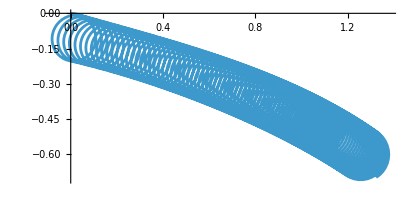

```mathematica
Xexpr =((X/.rules)/.sol00/.sol01/.sol10/.sol11)[t]
zexpr = ((z/.rules)/.sol00/.sol01/.sol10/.sol11)[t]
(*WAIT DELTA DEPENDS ON EPSILON VIA M THIS IS A PROBLEM YOU NEED TO FIX!*)
Variables[Xexpr]
St = .1;
M = (1-I*St-St*vS)/(eps*b)
params = {eps->0.1,delta->,vS->0.001,b->0.9,St->0.1};
ParametricPlot[Evaluate[{Xexpr+t,zexpr}/.params],{t,0,500},PlotRange->All]
```

```mathematica
(*Plot this with sample parameters…*)
```